# Exporter Test

### generate a graph to test on

#### Twine HTML Parser

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineParser]
twineParser[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,assocForm,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
]

]
twineParser::usage = "twineParser[path/to/file.html] gives a graph of a Twine 2 project";
```

```mathematica
?twineParser
```

twineParser[path/to/file.html] gives a graph of a Twine 2 project

#### Association Form

```mathematica
Clear[twineToAssociation]
twineToAssociation[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,completeAssociation,edges,alledges, g, v},
(*Import Twine Project as string*)
fileAsString = Import[absoluteFilePath, "String"];

(*Explicitly Parse XML | Riccardo's Algorithm*)
xmlObject = parseXML[fileAsString];

(*Get the root node*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];

(*Extract the Story name*)
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;

(*Extract the passages in the form {passage-name, content}*)
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];

(*Create Assocation between passage and content for tooltips and remove the link syntax*)
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Root Node Association*)
rootAssociation = <|rootNodeName -> "Start Here"|>;
(*Add rootnode pair to association*)
completeAssociation =AssociateTo[rootAssociation,passageContentThread];
]
twineToAssociation::usage = "twineToAssociation[path/to/file.html] Generates an Assocation of a Twine 2 project";
```

```mathematica
?twineToAssociation
```

twineParser[path/to/file.html] Generates an Assocation of a Twine 2 project

```mathematica
test=twineToAssociation["~/Documents/Twine/Stories/TwineBridge_Test.html"]
```

{TwineBridge_Test→Start Here,First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! }

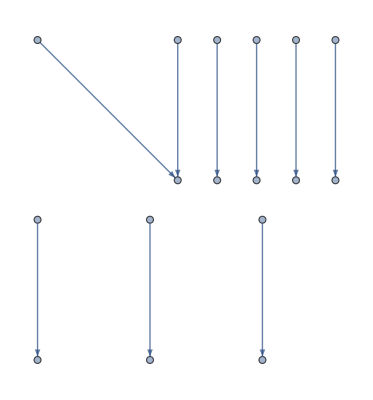

```mathematica
Graph[test]
```

#### Graphs

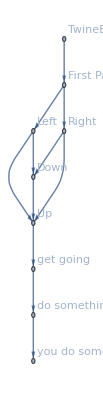

```mathematica
graph1=twineParser["~/Documents/Twine/Stories/TwineBridge_Test.html"]
graph2 = twineParser["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"];
graph3 = twineParser["~/Documents/Twine/Stories/TwineBridge_Test-Medium.html"];
GraphicsRow[{graph1, graph2, graph3}]
```

ONLY PUBLISHED TWINE 2 STORIES WILL WORK — so what does this mean, does that mean if i haven’t  published from twine it won’t work?

Root vertex is the story name. Every vertex, except the root is a passage. Here is a structure I need to follow:

#### Developing Export Procedure

```mathematica
?StringTemplate
```

StringTemplate[string] yields a TemplateObject expression that represents a string template to be applied to arguments. 
StringTemplate[src] uses File[…], URL[…] or CloudObject[…] as the source for the string template.
StringTemplate[form,args] yields a TemplateObject with arguments, suitable for cloud deployment or other evaluation.

— Convert the graph to an association
— Use StringTemplate to fill in data?
—Consider TreePlot

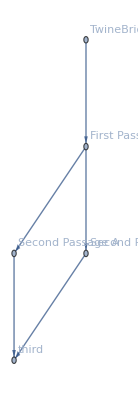

```mathematica
test
```

### Potential Procedure

From | Graph → Association → HTML

	Let’s look at the overall graph structure to see what patterns we need to pay attention to.
	
	What we need are the passage names and their content.
	
	Iterate over the passages to create their strings.

```mathematica
testAssociation = twineToAssociation["~/Documents/Twine/Stories/TwineBridge_Test.html"]
```

<|TwineBridge_Test→Start Here,First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

— Rule[“RootVertex”, <story-name>]
<tw-storydata name=”<story-name>” startnode=”1” creator=”WL-TwineBridge” creator-version=”0.01” zoom=”1” format=”Harlowe” format-version=”2.1.0” options=”” hidden>

—

The current workflow doesn’t make any sense, because the association needs to be created from a graph, not the html file.

#### StringTemplate

```mathematica
StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">

  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">

  </script>
"
][<|"storyTitle" -> First[Keys[%1167]]|>]
```

```mathematica
% <>"</tw-storydata>"
```

<tw-storydata name="TwineBridge_Test" startnode="1" creator="Twine" creator-version="2.2.1" zoom="1" format="Harlowe" format-version="2.1.0" options="" hidden>

  <style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">

  </style>
  <script role="script" id="twine-user-script" type="text/twine-javascript">

  </script>


</tw-storydata>

```mathematica
testAssociation
```

<|TwineBridge_Test→Start Here,First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
exportTwineProject[associationForm_Association, exportPathToFile_, fileName_]:=Module[{storyAssoc = associationForm , sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc =KeyDrop[testAssociation,First[Keys[testAssociation]]];
assocLength=Length[passageAssoc];
passages=Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"320,377\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧|>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>fileName<>".html",stringOfStory , "HTMLFragment"]
]
```

```mathematica
exportTwineProject[testAssociation,"~/Desktop/","fifthExport"]
```

~/Desktop/fifthExport.html

#### exportTwineProject[] needs to take in a graph as the first argument